```mathematica
S[α_]=FullSimplify[
Integrate[(1/π)^(1/2) ((2 α)/π)^(3/4) Exp[-r - α r^2] r^2,{r,0,Infinity},Assumptions->{α>0}],
Assumptions->{α>0}]
FindMaximum[S[x],{x,0.1}]
```

(-2 √α+ⅇ^(1/4/α) √π (1+2 α) Erfc[1/(2 √α)])/(4 2^(1/4) π^(5/4) α^(7/4))

{0.0778589,{x→0.27095}}

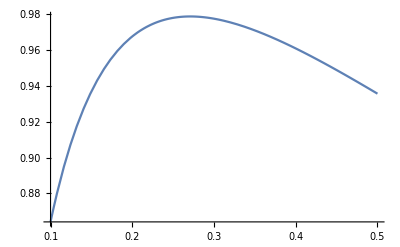

```mathematica
Plot[4π  S[α],{α,0.1,0.5}]
```